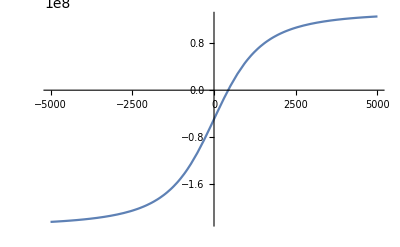

2.85249

```mathematica
(*NOTE - THIS IS WORKING IN THE ROTATING FRAME, NOT THE IDLING FRAME OR THE LAB FRAME*)

setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;

Plot[δRot[1, 2], {ΔE, -5000, 5000}]

echoRate = .0106;
Tmax = 7*10^-9 + echoRate/(π*A*d*e/(2*h*Vt));
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 10000*Min[1, T1/(5*10^-9)];
δE = 1;
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= findEvolutionOperator[Hcorrected, Tmax];

Zangle[U_] := ArcTan[Re[U[[1, 1]]/U[[2, 2]]], Im[U[[1, 1]]/U[[2, 2]]]]

Zangle[U /. t->Tmax]

clearVariables[];
```

```mathematica
gateDecompositionParameters[{{1, 0}, {0, E^ⅈ}}]
```

{-1/2+2 π,0,-1/2+2 π,1/2,1.}